# STROŠKI OLIMPIJSKIH IGER

## Analiza stroškov olimpijskih iger med leti 1964 in 2016

## Pridobivanje podatkov

```mathematica
ResourceSearch["Olympic Games"]
```

{ResourceObject[…]}

Shranimo podatke:

```mathematica
vsiPodatki = ResourceData["Olympic Games Costs"]
```

Dataset[<>]

Tiste Olimpijske Igre, za katere ni bilo podatkov o stroških, sem izbrisal iz tabele. Kjer bom analiziral stroške, jih ne bom upošteval.

```mathematica
podatki = Select[vsiPodatki, !MissingQ[#Cost]&];
```

```mathematica
poletneIgre = Select[podatki, #["Type"] ==  "Summer" &];
```

```mathematica
zimskeIgre = Select[podatki, #["Type"] ==  "Winter" &];
```

## Analiza stroškov

Spodaj vidimo grafa, ki predstavljata stroške na posameznih Olimpijskih Igrah. Na zgornjem grafu so poletne igre, na spodnjem pa zimske. Pričakoval sem, da bodo stroški pri kasnejših Olimpijskih Igrah večji,  vendar tukaj to ni res. Že, na primer,  leta 1976 so bili stroški večji kot leta 2016, in celo dvakrat večji kot leta 2004. Vidimo, da po višini stroškov iztopajo dvoje Olimpijske Igre. Pri poletnih je bilo največ stroškov v Londonu, pri zimskih pa daleč največ v Sočiju.

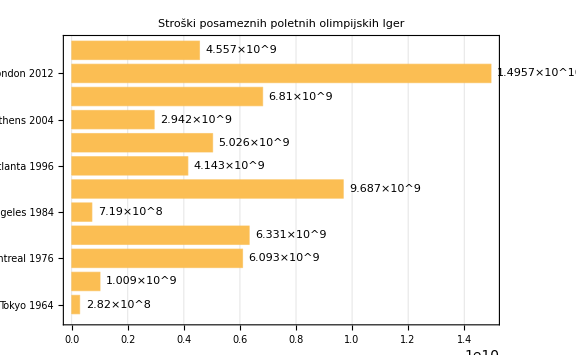

```mathematica
r1 = BarChart[poletneIgre[All, "Cost"], ChartLabels->{poletneIgre[All, "Games"]//Normal},LabelingFunction->After, PlotLabel->"Stroški posameznih poletnih olimpijskih Iger", ImageSize->Large, BarSpacing->Medium, PlotTheme->"Detailed", BarOrigin->Left]
```

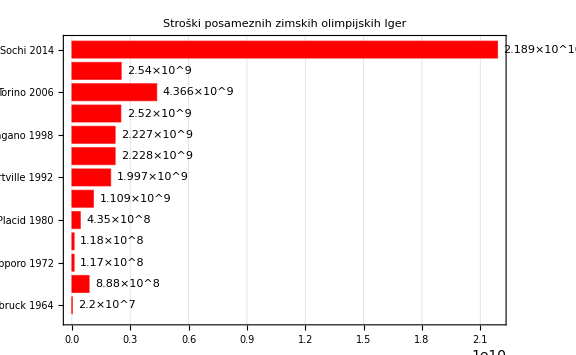

```mathematica
r2 = BarChart[zimskeIgre[All, "Cost"], ChartLabels->{zimskeIgre[All, "Games"]//Normal},LabelingFunction->After, PlotLabel->"Stroški posameznih zimskih olimpijskih Iger", ImageSize->Large, BarSpacing->Medium, PlotTheme->"Detailed", ChartStyle->{Red}, BarOrigin->Left]
```

Sedaj bom stroške zimskih in poletnih Iger združil v en graf. Pikice bom med sabo povezal, da se bo leepše videlo razliko v stroških. Vidimo, da so bili stroški na poletnih Igrah večji kot na zimskih. Izjema je Soči, ki je v tej kategoriji daleč pred vsemi.

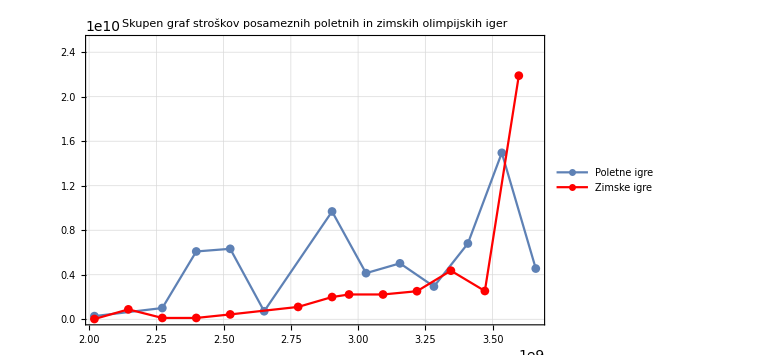

```mathematica
g1 = DateListPlot[poletneIgre[All, {"Year", "Cost"}], PlotTheme->"FullAxesGrid", ImageSize->Large,PlotRange->{0, 2.5*10^10},PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic];
g2 = DateListPlot[zimskeIgre[All, {"Year", "Cost"}], PlotTheme->"FullAxesGrid", ImageSize->Large, PlotRange->{0, 2.5*10^10}, PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic];
Show[g1, g2, PlotLabel->"Skupen graf stroškov posameznih poletnih in zimskih olimpijskih iger", ImageSize->Large]
```

Da so stroški poletnih OI veliko večji, je razumljivo, saj lahko vidimo, da je na poletnih OI tudi veliko več dogodkov.

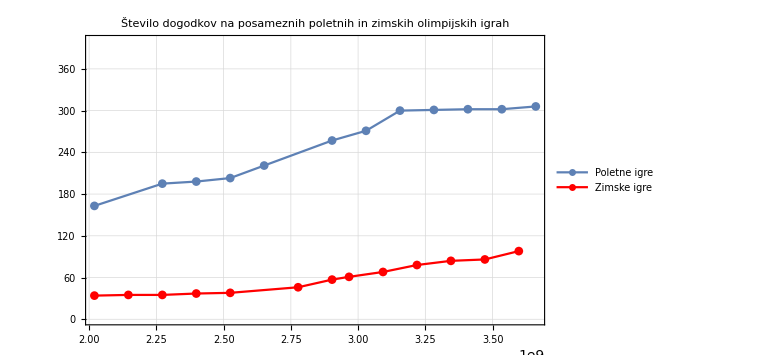

```mathematica
f1 = DateListPlot[poletneIgre[All, {"Year", "Events"}], PlotLabel->"Število dogodkov na posameznih poletnih olimpijskih igrah", PlotTheme->"FullAxesGrid", ImageSize->Medium, PlotRange->{0, 400},PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic];
f2 = DateListPlot[zimskeIgre[All, {"Year", "Events"}],  PlotLabel->"Število dogodkov na posameznih zimskih olimpijskih igrah", PlotTheme->"FullAxesGrid", ImageSize->Medium, PlotRange->{0, 400},PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic];
Show[f1, f2,  PlotLabel->"Število dogodkov na posameznih poletnih in zimskih olimpijskih igrah", ImageSize->Large]
```

V podatkih manjka podatek o stroških na dogodek na OI v Sočiju. Ker imamo podatek o tem kolikšni so bili absolutni stroški, in koliko je bilo dogodkov, lahko zdaj z lahkoto izračunamo tudi stroške na dogodek. Potem lahko tudi dopolnemo tabelo.

```mathematica
stroskiRusija = Round[Select[podatki, #["Games"] ==  "Sochi 2014" &][1, "Cost"] / Select[podatki, #["Games"] ==  "Sochi 2014" &][1, "Events"]]
```

223367347 $

Dodajmo našim podatkom še stroške na dogodek v Sočiju.

```mathematica
niz = Normal[zimskeIgre[All, {"Games", "Year", "CostPerEvent"}]]
```

{<|Games→Innsbruck 1964,Year→Year: 1964,CostPerEvent→600 000.00 $|>,<|Games→Grenoble 1968,Year→Year: 1968,CostPerEvent→2.54e7 $|>,<|Games→Sapporo 1972,Year→Year: 1972,CostPerEvent→3.4e6 $|>,<|Games→Innsbruck 1976,Year→Year: 1976,CostPerEvent→3.2e6 $|>,<|Games→Lake Placid 1980,Year→Year: 1980,CostPerEvent→1.15e7 $|>,<|Games→Calgary 1988,Year→Year: 1988,CostPerEvent→2.41e7 $|>,<|Games→Albertville 1992,Year→Year: 1992,CostPerEvent→35000000 $|>,<|Games→Lillehammer 1994,Year→Year: 1994,CostPerEvent→3.65e7 $|>,<|Games→Nagano 1998,Year→Year: 1998,CostPerEvent→3.2700000000000004e7 $|>,<|Games→Salt Lake City 2002,Year→Year: 2002,CostPerEvent→2.33e7 $|>,<|Games→Torino 2006,Year→Year: 2006,CostPerEvent→52000000 $|>,<|Games→Vancouver 2010,Year→Year: 2010,CostPerEvent→2.95e7 $|>,<|Games→Sochi 2014,Year→Year: 2014,CostPerEvent→Missing[NotAvailable]|>}

Ker v podatkih manjka samo en podatek, ga lahko zamenjamo kar tako:

```mathematica
popravljeno = ReplacePart[niz, Position[niz,Missing["NotAvailable"]]-> stroskiRusija]
```

{<|Games→Innsbruck 1964,Year→Year: 1964,CostPerEvent→600 000.00 $|>,<|Games→Grenoble 1968,Year→Year: 1968,CostPerEvent→2.54e7 $|>,<|Games→Sapporo 1972,Year→Year: 1972,CostPerEvent→3.4e6 $|>,<|Games→Innsbruck 1976,Year→Year: 1976,CostPerEvent→3.2e6 $|>,<|Games→Lake Placid 1980,Year→Year: 1980,CostPerEvent→1.15e7 $|>,<|Games→Calgary 1988,Year→Year: 1988,CostPerEvent→2.41e7 $|>,<|Games→Albertville 1992,Year→Year: 1992,CostPerEvent→35000000 $|>,<|Games→Lillehammer 1994,Year→Year: 1994,CostPerEvent→3.65e7 $|>,<|Games→Nagano 1998,Year→Year: 1998,CostPerEvent→3.2700000000000004e7 $|>,<|Games→Salt Lake City 2002,Year→Year: 2002,CostPerEvent→2.33e7 $|>,<|Games→Torino 2006,Year→Year: 2006,CostPerEvent→52000000 $|>,<|Games→Vancouver 2010,Year→Year: 2010,CostPerEvent→2.95e7 $|>,<|Games→Sochi 2014,Year→Year: 2014,CostPerEvent→223367347 $|>}

```mathematica
tabelaStroskovNaDogodek = Dataset[popravljeno];
```

Kaj pa stroški na dogodek.

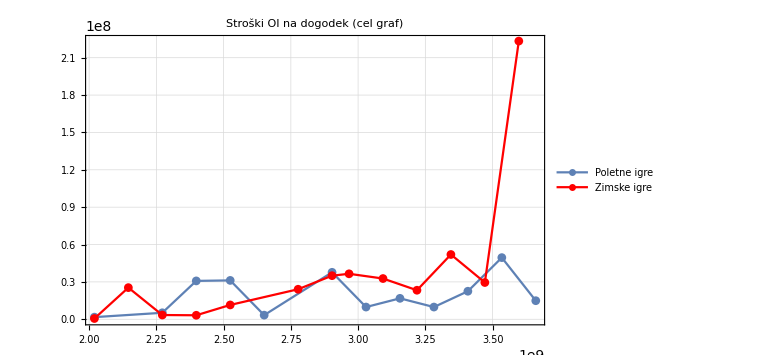

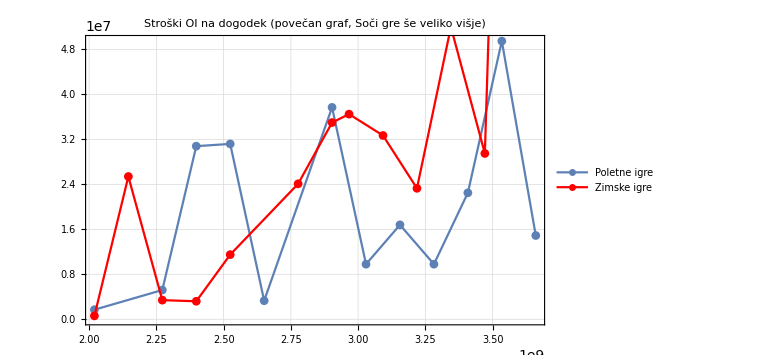

```mathematica
z1 = DateListPlot[poletneIgre[All, {"Year", "CostPerEvent"}], PlotLabel->"Stroški poletnih olimpijskih iger na posamezni dogodek", PlotTheme->"FullAxesGrid", ImageSize->Medium,PlotLegends->LineLegend[{"Poletne igre"}], PlotMarkers->Automatic];
z2 = DateListPlot[tabelaStroskovNaDogodek[All, {"Year", "CostPerEvent"}], PlotLabel->"Stroški zimskih olimpijskih iger na posamezni dogodek", PlotTheme->"FullAxesGrid", ImageSize->Medium,PlotRange->{0, 223367347}, PlotLegends->LineLegend[{"Zimske igre"}], PlotStyle->Red, PlotMarkers->Automatic];
Show[z1, z2,PlotLabel->"Stroški OI na dogodek (cel graf)", PlotRange->{0, 223367347},ImageSize->Large]
Show[z1, z2, PlotLabel-> "Stroški OI na dogodek (povečan graf, Soči gre še veliko višje)",ImageSize->Large]
```

Grafa se veliko sekata, torej vidimo, da so stroški na dogodek bolj primerljivi. Olimpijske igre v Sočiju sedaj izstopajo še veliko bolj kot pri absolutnih stroških.

```mathematica
x= Normal[podatki[All, {"Games", "Year", "CostPerEvent"}]];
```

```mathematica
y= Dataset[ReplacePart[x, Position[x,Missing["NotAvailable"]]-> stroskiRusija]]
```

Dataset[<>]

Stroški na dogodek, vidimo da sta tukaj isti dve državi.

```mathematica
Select[y,#["CostPerEvent"] == Max[y[All, "CostPerEvent"]]&]
```

Dataset[<>]

```mathematica
Select[y,#["CostPerEvent"] == Min[y[All, "CostPerEvent"]]&]
```

Dataset[<>]

## Gostiteljice iger med leti 1960 in 2016

Tukaj so vse države, ki so gostile OI med tema dvema letoma

```mathematica
vsiPodatki[Select[Head[#["Country"]]=!=Failure&],"Country"]
```

Dataset[<>]

```mathematica
Select[vsiPodatki,!MissingQ[#CountryEntity]&]
```

Dataset[<>]

Tukaj so vse države, ki še obstajajo. Kot vidimo ni Sovjetske zveze in Jugoslavije.

```mathematica
seznamDrzav=Select[vsiPodatki, !MissingQ[#CountryEntity]&][Select[Head[#["CountryEntity"]]=!=Failure&],"CountryEntity"]
```

Dataset[<>]

```mathematica
Select[podatki, #["CountryEntity"] ==  Missing["NotAvailable"]&][All, {"Country", "Games"}]
```

Dataset[<>]

Spodaj vidimo koliko OI med letoma 1960 in 2016, je gostila posamezna država.

```mathematica
gostiteljice[drzava_]:={drzava,Count[seznamDrzav,drzava]}
```

```mathematica
kolikokratGostiteljice=gostiteljice/@(seznamDrzav//DeleteDuplicates)
```

Dataset[<>]

```mathematica
Normal[kolikokratGostiteljice]
```

{{Italy,2},{Japan,3},{Mexico,1},{Germany,1},{Canada,3},{United States,5},{South Korea,1},{Spain,1},{Australia,1},{Greece,1},{China,1},{United Kingdom,1},{Brazil,1},{Austria,2},{France,2},{Norway,1},{Russia,1}}

Seznam popravimo ročno. Dvoje igre v zgornjem seznamu še manjkajo, saj državi, ki sta jih gostili ne obstajata več. Za igre iz Sovjetske zveze bomo rekli, da so bilev Rusiji, saj je bila gostiteljica Moskva. Za igre iz Yugoslavije pa sem vzel kar Bosno in Hercegovino, saj so bile takrat igre v Sarajevu.

```mathematica
seznamGostiteljic = {Entity["Country","Italy"]-> 2,Entity["Country","Japan"]-> 3,Entity["Country","Mexico"]-> 1,Entity["Country","Germany"]-> 1,Entity["Country","Canada"]-> 3,Entity["Country","UnitedStates"]-> 5,Entity["Country","SouthKorea"]-> 1,Entity["Country","Spain"]-> 1,Entity["Country","Australia"]-> 1,Entity["Country","Greece"]-> 1,Entity["Country","China"]-> 1,Entity["Country","UnitedKingdom"]-> 1,Entity["Country","Brazil"]-> 1,Entity["Country","Austria"]-> 2,Entity["Country","France"]-> 2,Entity["Country","Norway"]-> 1,Entity["Country","Russia"]-> 2, Entity["Country","BosniaHerzegovina"]-> 1}
```

{Italy→2,Japan→3,Mexico→1,Germany→1,Canada→3,United States→5,South Korea→1,Spain→1,Australia→1,Greece→1,China→1,United Kingdom→1,Brazil→1,Austria→2,France→2,Norway→1,Russia→2,Bosnia and Herzegovina→1}

Na zemljevidu vidimo katere države so gostile olimpijske igre med letoma 1960 in 2016, ter katere so jih gostile večkrat.

```mathematica
GeoRegionValuePlot[seznamGostiteljic, GeoRange->"World", GeoProjection->"Mercator", ImageSize->Large, GeoBackground->"CountryBorders"]
```

-Graphics-

```mathematica
Amerika = Select[podatki, MemberQ[EntityList[EntityClass["Country","EuropeanUnion"]],#["Country"]]&]
```

Dataset[<>]

## Analiza olimpijskih iger v Ameriki

```mathematica
prvo =Select[kolikokratGostiteljice,#[[2]]==Max[kolikokratGostiteljice[All,2]]&]
```

Dataset[<>]

Vidimo, da je država, ki je med letoma 1960 in 2016 največkrat gostila olimpijske igre Amerika. Gostila jih je petkrat.

```mathematica
usa = Select[vsiPodatki, #["CountryEntity"]==LinguisticAssistant &]
```

Dataset[<>]

Združene države so gostile dvoje poletne in tri zimske igre.

```mathematica
Length[Select[usa, #["Type"] ==  "Summer" &]]
```

2

```mathematica
Length[Select[usa, #["Type"] ==  "Winter" &]]
```

3

```mathematica
vrednosti = #["Games"]-> #["Cost"]& /@podatki
```

Dataset[<>]

```mathematica
data=QuantityArray[EntityValue[EntityClass["Element",All],{"AtomicMass","MeltingPoint"}]]
```

```mathematica
GeoRegionValuePlot[SteviloPoDrzavah,PlotLabel->"Število usmrtitev po državah v ZDA",GeoLabels->Automatic,ImageSize->{1200,600},ColorFunction->"TemperatureMap"]
```

GeoRegionValuePlot::noents: no valid location -> value pairs found

Infinity::indet: Indeterminate expression -∞+∞ encountered.

-Graphics-

```mathematica
GeoRegionValuePlot[CountryData["OECD"]->"GDPPerCapita",ImageSize->1200]
```

```mathematica
GeoRegionValuePlot[First@Keys@#->Total[Values@#]&/@GatherBy[#"Country/City"->#DailyProduction&/@ResourceData["Top Oil Fields 2001"],First]]
```

```mathematica
nizDrzav = Normal[seznamDrzav]
```

{Italy,Japan,Mexico,Germany,Canada,United States,South Korea,Spain,United States,Australia,Greece,China,United Kingdom,Brazil,United States,Austria,France,Japan,Austria,United States,Canada,France,Norway,Japan,United States,Italy,Canada,Russia}

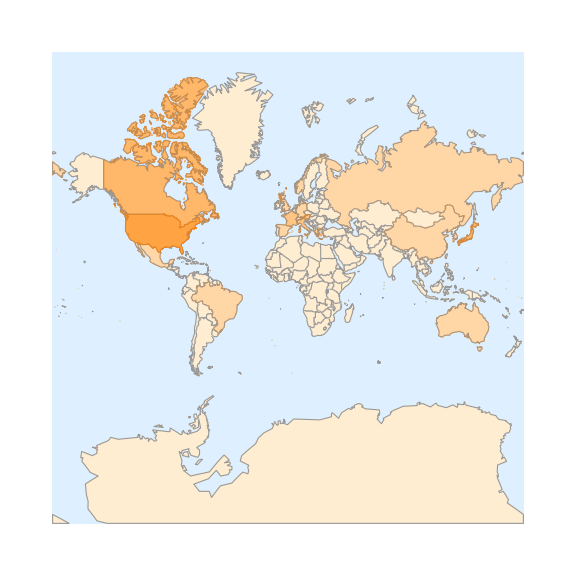

```mathematica
GeoGraphics[{Orange, Polygon[nizDrzav]}, GeoRange->"World", GeoProjection->"Mercator", ImageSize->Large, GeoBackground->"CountryBorders"]
```

```mathematica
kolikokratGostiteljice[All,1]->kolikokratGostiteljice[All,2]
```

Dataset[<>]→Dataset[<>]

Olimpijske igre z največjimi in najmanjšimi stroški.

```mathematica
Select[podatki,#["Cost"] == Max[podatki[All, "Cost"]]&]
```

Dataset[<>]

```mathematica
Select[podatki,#["Cost"] == Min[podatki[All, "Cost"]]&]
```

Dataset[<>]

## Aplikacija v oblaku

```mathematica
prikazPodatkov[drzava_]:= StringForm["Between the 1960 and 2016 `` hosted Olympic Games ``-times. Tabele, with more data: ``",Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&][1, "Country"],Length[Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&]],Select[ResourceData["Olympic Games Costs"], #["CountryEntity"]==drzava&]]
```

```mathematica
obrazec = FormPage["drzava" -> "Country", prikazPodatkov[#drzava] &,AppearanceRules-><|"Title" -> "Gostitelji olimpijskih iger", "Description" -> "Vnesi ime drzave, za katero zelis izvedeti, kolikokrat je med leti 1960 in 2016 gostila olimpijske igre, ter podrobnosti teh iger.", "SubmitLabel" -> "Prikazi"|>]
```

```mathematica
CloudDeploy[obrazec, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/a3abd79b-a0c7-47a8-92d5-e9ae3924c703]